### Functions

```mathematica
ClearAll[PDFX];
PDFX[n_,x_]:=((1-x^2)^(1/2 *(n-3))*Gamma[n/2])/(Sqrt[Pi]*Gamma[(n-1)/2]);
```

```mathematica
ClearAll[HxShow];
HxShow[X_,j_,Hr_]:=Module[{i,n,r,d,Pn,Hc,Hs,Hp,Xmin,Xmax},
Pn=Length[X];n=Length[X[[1]]];
Xmin=-1.0;Xmax=+1.0;d=N[Xmax-Xmin];
Hs=d/N[Hr-1];Hc=Array[{Xmin+Hs(#-1),0}&,Hr];
Hs=N[Hr]/d;For[i=1,i<=Pn,i++,
r=1+IntegerPart[Hs*(X[[i,j]]-Xmin)];
r-=If[r==Hr,1,0];Hc[[r,2]]++];
Hs=2.0*N[Pn]/N[Hr];Hp=Array[{d=Hc[[#,1]],Hs*PDFX[n,d]}&,Hr];
ListPlot[{Hp,Hc},PlotRange-> All,Frame->True,FrameLabel->{"X", "count"},
PlotLabel->StringJoin[Map[ToString,{"X[",j,"] PDF: ",{n,Pn}}]],
PlotStyle->{Gray,Blue},ImageSize->Medium]];
```

```mathematica
ClearAll[RoShow];
RoShow[Ro_,Rn_,Pn_]:=Module[{s},
s=StringJoin[Map[ToString,{Rn,"D(S) →  ",Rn-2,"D(V), ",Pn," points"}]];
ListLinePlot[Ro,AxesOrigin->{0,1},PlotRange-> All,Frame->True,
FrameLabel->{"(r,  distance)/(bound radius)","(P (r))/even"},PlotLabel->s,ImageSize->Medium]];
```

```mathematica
Clear[PtShow];
PtShow[X_,R_:1]:=Module[{s,p,Rt,Rg,Pn,Rn},
Rt=0.6/√Pn;Rg=R+Rt;Pn=Length[X];Rn=Length[X[[1]]];
s=StringJoin[Map[ToString,{Rn,"D(S) → 2D(V), ",Pn," points"}]];
Return[Graphics[{Table[{Hue[RandomReal[{0.5,0.9}]],Ball[X[[p,{1,2}]],Rt]},{p,1,Pn}]},
PlotRange->Array[{-Rg,+Rg}&,2],PlotLabel->s,ImageSize->Medium]]];
```

```mathematica
Clear[DsShow];
DsShow[Hn_:200,Ls_,Rn_,Rb_]:=Module[{i,j,s,H,K,S,P,V},
H=Array[0&,Hn]; P=Length[Ls];K=Hn/(2Rb);S=2/Hn;V=(2 Hn)/(P(P-1));
For[i=1,i≤ P,i++,For[j=i+1,j≤ P,j++,H[[Ceiling[K Ls[[i,j]]]]]++]];
s=StringJoin[Map[ToString,{Rn,"D(S) → 1D(ρ), ",P," points, ",P(P-1)/2," distaces"}]];
ListPlot[
Table[{S i,V H[[i]]},{i,Hn}],PlotRange-> All,FrameLabel->{"(ρ,  distance)/(bound radius)","(P (ρ))/even"},
PlotLabel->s,Joined->True,Frame->True]];
```

```mathematica
Clear[DpShow];
DpShow[Hn_:200,Xs_,Rn_,Rb_,Rp_:2]:=Module[{i,s,r,H,K,S,P,V},
H=Array[0&,Hn]; P=Length[Xs];K=Hn/Rb;S=1/Hn;V=(Hn Rb)/(P Rp);
For[i=1,i≤ P,i++,r=Take[Xs[[i]],Rp];H[[Ceiling[K √(r.r)]]]++];
s=StringJoin[Map[ToString,{Rn,"D(S) → , ",Rp,"D(V), ",P," points"}]];
ListPlot[
Table[{S i,(Rb/(S i))^(Rp-1)V H[[i]]},{i,Hn}],AxesOrigin->{0,1},ImageSize->Medium,
PlotRange-> All,FrameLabel->{"(r,  distance)/(bound radius)","(P (r))/even"},PlotLabel->s,Joined->True,Frame->True]];
```

```mathematica
Clear[DvShow];
DvShow[Hn_:200,Xs_,Rn_,Rb_,Rp_:2]:=Module[{i,s,r,H,K,S,P,V},
H=Array[0&,Hn]; P=Length[Xs];K=Hn/Rb;S=1/Hn;V=(Hn Rb)/(P Rp);
For[i=1,i≤ P,i++,r=Take[Xs[[i]],Rp];H[[Ceiling[K √(r.r)]]]++];
s=StringJoin[Map[ToString,{Rn,"D(C) → , ",Rp,"D(V), ",P," points"}]];
ListPlot[
Table[{S i,(Rb/(S i))^(Rp-1)V H[[i]]},{i,Hn}],AxesOrigin->{0,1},
PlotRange-> All,FrameLabel->{"(r,  distance)/(bound radius)","(P (r))/even"},PlotLabel->s,Joined->True,Frame->True]];
```

```mathematica
ClearAll[RandomSphere]; 
RandomSphere=Compile[{{Rn,_Integer},{Pn,_Integer},{Rb,_Real}},
Module[{i,j,m,p,r,s,S,X,Xi,Xj,rr,RD},
X=Array[N[0]&,{Pn,Rn}];s=N[1/√2];RD=N[1];
For[p=1,p≤ Pn,p++,i=RandomInteger[{1,Rn}];X[[p,i]]=RandomChoice[{-1,1}];
S=N[1];For[r=1,r≤ Rn,r++,If[r==i,Continue[]];
rr=RandomReal[{-RD,RD}];S+=rr*rr;X[[p,r]]=rr];
X[[p]]*=Rb/√S;
For[m=1,m≤ Rn,m++,
i=RandomInteger[{1,Rn}];j=i;While[i==j,j=RandomInteger[{1,Rn}]];
Xi=X[[p,i]];
Xj=X[[p,j]];
X[[p,i]]=s (Xj-Xi);
X[[p,j]]=s (Xj+Xi)]];Return[X]],"RuntimeOptions"->"Speed"];

(*Needs["CompiledFunctionTools`"];CompilePrint[RandomSphere]*)
```

### 4D(S)→2D(V), Import

<X^2> = {0.25036, 0.248968, 0.249981, 0.250691}

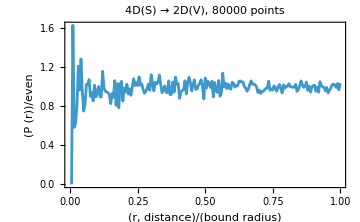
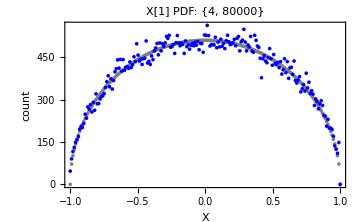
-Graphics- | -Graphics-
-Graphics- | *4D(S)*

```mathematica
Rn=4;Rb=1; Fn=NotebookDirectory[]<>"Rep-04-80000";
data=Import[Fn<>".json","RawJSON"];
X=data["values"];Ro=data["density"];ClearAll[data]; Pn=Length[X];
S="<X^2> = "<>ToString[Array[Sum[X[[p,#]]^2,{p,1,Pn}]/Pn&,Rn]]
Grid[{
{RoShow[Ro,Rn,Pn],Show[Import[Fn<>".png"],ImageSize->Small]},
{HxShow[X,1,200],"*"<>ToString[Rn]<>"D(S)*"}}]
```

```mathematica
(*Wiki article, n-segment*)
(*Column[
{RoShow[Ro,Rn,Pn],Show[Import[Fn<>".png"],ImageSize->Small],HxShow[X,1,200]},Alignment->Center]*)
```

### 8D(S)→6D(V), Import

<X^2> = {0.124534, 0.12425, 0.127727, 0.12507, 0.123991, 0.120039, 0.129459, 0.124929}

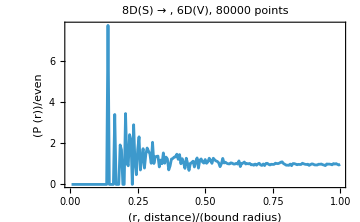
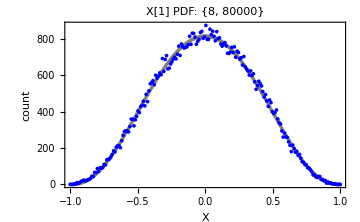
-Graphics- | -Graphics-
-Graphics- | *8D(S)*

```mathematica
Rn=8;Rb=1; Fn=NotebookDirectory[]<>"Rep-08-80000";
data=Import[Fn<>".json","RawJSON"];
X=data["values"];Ro=data["density"];ClearAll[data]; Pn=Length[X];
S="<X^2> = "<>ToString[Array[Sum[X[[p,#]]^2,{p,1,Pn}]/Pn&,Rn]]
Grid[{
{RoShow[Ro,Rn,Pn],Show[Import[Fn<>".png"],ImageSize->Small]},
{HxShow[X,1,200],"*"<>ToString[Rn]<>"D(S)*"}}]
```

{8,0}	{7,0}	{6,0}	{5,11}

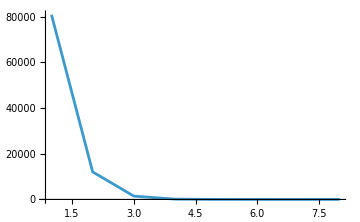
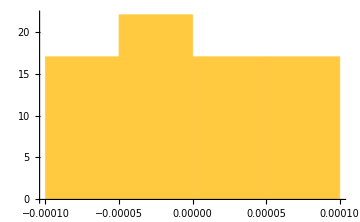

```mathematica
ClearAll[Rp,H,i,x,c,d];H=Array[{0,0}&,Rn];(*0.1^2=0.01*)

For[d=1,d<=Rn,d++,c=0;Rp=Rn-d+1;ClearAll[x];x=Array[0&,Rp];
For[i=1,i<=Pn,i++,x=Take[X[[i]],{d,Rn}];If[x.x<0.01,c++]];H[[Rp]]={Rp,c}];

Print[H[[Rn-0]],"\t",H[[Rn-1]],"\t",H[[Rn-2]],"\t",H[[Rn-3]]];
i=1;Row[{
ListLinePlot[H,PlotRange->All,ImageSize->Medium],
Histogram[Select[Array[X[[#,i]]&,Pn],Abs[#]<0.0001&],ImageSize->Medium]}]
```

### 12D(S)→10D(V), Import

<X^2> = {0.0908761, 0.0834907, 0.0833968, 0.0803329, 0.0832431, 0.0848949, 0.0796974, 0.0843082, 0.0811997, 0.084334, 0.0800378, 0.0841884}

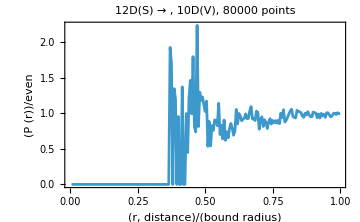
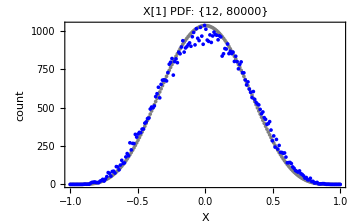
-Graphics- | -Graphics-
-Graphics- | *12D(S)*

```mathematica
Rn=12;Rb=1; Fn=NotebookDirectory[]<>"Rep-12-80000";
data=Import[Fn<>".json","RawJSON"];
X=data["values"];Ro=data["density"];ClearAll[data]; Pn=Length[X];
S="<X^2> = "<>ToString[Array[Sum[X[[p,#]]^2,{p,1,Pn}]/Pn&,Rn]]
Grid[{
{RoShow[Ro,Rn,Pn],Show[Import[Fn<>".png"],ImageSize->Small]},
{HxShow[X,1,200],"*"<>ToString[Rn]<>"D(S)*"}}]
```

```mathematica
ClearAll[H,x,c,d];H=Array[{0,0}&,Rn];(*0.3^2=0.09*)
For[d=1,d<Rn,d++,c=0;Rp=Rn-d;ClearAll[x];x=Array[0&,Rp];
For[i=1,i<=Pn,i++,x=Take[X[[i]],{d,Rn}];If[x.x<0.09,c++]];H[[Rp]]={d,c}];
Print[H[[Rn-0]],"\t",H[[Rn-1]],"\t",H[[Rn-2]],"\t",H[[Rn-3]]];

Row[{
ListLinePlot[H,PlotRange->All,ImageSize->Small],
Histogram[Array[X[[#,1]]&,Pn],ImageSize->Medium],
Histogram[Select[Array[X[[#,1]]&,Pn],Abs[#]<0.0001&],ImageSize->Medium]}]
```

### 12D(S)→10D(V)

```mathematica
Rn=4;Pn=10000;Rp=Rn-2;Rb=1;
X=RandomSphere[Rn,Pn,Rb];
S="<X^2> = "<>ToString[Array[Sum[X[[p,#]]^2,{p,1,Pn}]/Pn&,Rn]]
Grid[{{DpShow[200,X,Rn,Rb,Rp],PtShow[X,Rb]}}]
```

### Drafts

```mathematica
(*Volume density function*)
Clear[r,R,Pn,Rn];
Integrate[(Pn Rn)/R(r/R)^(Rn-1),{r,0,R},Assumptions->And[{R>0,Rn>0}]]
```

```mathematica
ClearAll[r,n,x, Vdome,Vball,Ddome];(*Ball PDF*)

Vball[r_,n_]:=r^n Pi^(n/2)/Gamma[n/2+1];
FullSimplify[r Vball[r,n-1]/Vball[r,n]]

(*relative Vball[r, n]*)
Vdome[r_,n_,h_]:=Gamma[1+n/2]/(√Pi Gamma[(n+1)/2])Integrate[(1-x^2)^((n-1)/2),{x,(r-h)/r,1}];
(* h = x r + r*)
Ddome[n_,x_]:=((1-x^2)^(1/2 (n-1)) Gamma[1+n/2])/(Sqrt[Pi]*Gamma[(n+1)/2]);

Print["PDF integration test: ",Integrate[Ddome[n,x],{x,-1,+1},Assumptions->n>1]];
```

Gamma[1+n/2]/(√π Gamma[(1+n)/2])

PDF integration test: 1

```mathematica
ClearAll[r,n,x, Sdome,Sball,Vball,Ddome];(*Sphere PDF*)

Sball[r_,n_]:=r^(n-1)2 Pi^(n/2)/Gamma[n/2];
Vball[r_,n_]:=r^n Pi^(n/2)/Gamma[n/2+1];
FullSimplify[(n-1) Vball[r,n-1]/Sball[r,n]]
FullSimplify[(n-1) Vball[r,n-1]/Vball[r,n-2]]

(*relative Vball[r, n]*)
Sdome[r_,n_,h_]:=Gamma[n/2]/(√Pi Gamma[(n-1)/2])Integrate[(1-x^2)^((n-3)/2),{x,(r-h)/r,1}];
(* h = x r + r*)
Ddome[n_,x_]:=((1-x^2)^(1/2 (n-3)) Gamma[n/2])/(Sqrt[Pi]*Gamma[(n-1)/2]);

Print["PDF integration test: ",Integrate[Ddome[n,x],{x,-1,+1},Assumptions->n>1]];
```

Gamma[n/2]/(√π Gamma[1/2 (-1+n)])

(2 √π r Gamma[n/2])/Gamma[1/2 (-1+n)]

PDF integration test: 1